-10.6151

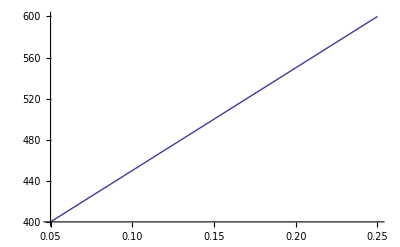

```mathematica
(* PLANE WALL *)
(* Incropera and Dewitt Ch. 3 - p. 134 *)

k =3.46;
(* W/m2K using water *)
x1=0.05;
x2= 0.25;
L = x2-x1;
(* cm  *)

a=0.25;
Dia=a*x2;
(* cm  *)
A = π*Dia^2/4;
(* 1 meter ^2  *)
R = L/(k*A);
(* Resistance  *)
(* Temperature on one side of wall *)
Subscript[T, 1]= 400;
(* Temperature on the other side of the wall *)
Subscript[T, 2]=600;

Q = (Subscript[T, 1]-Subscript[T, 2])/R
(* Watts / m^2  *)

T = Subscript[T, 1]+ (Subscript[T, 2]-Subscript[T, 1])*((x-x1)/(x2-x1));

Plot1=Plot[T,{x,.05,0.25},PlotRange->All]
```

```mathematica
(* Conical System D = 0.25*x *)
(* Incropera and Dewitt Ch. 3 - p. 134 *)
```

-2.12303

-33.9685 x^2

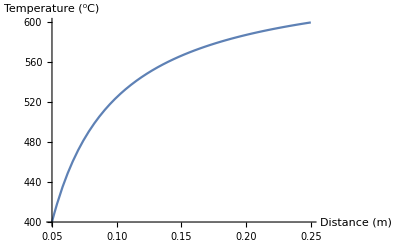

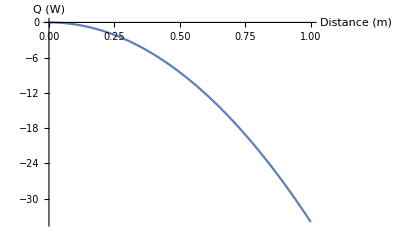

```mathematica
k = 3.46;
(* W/m2K using water *)

x1=0.05;
x2= 0.25;
L = x2-x1;
a=0.25;
Dia=a*x;
(* cm  *)
A = π*Dia^2/4;
(* 1 meter ^2  *)
R = L/(k*A);
(* Resistance  *)
(* Temperature on one side of wall *)
Subscript[T, 1]= 400;
(* Temperature on the other side of the wall *)
Subscript[T, 2]=600;

Q =π*a^2*k*(Subscript[T, 1]-Subscript[T, 2])/(4((1/x1)-(1/x2)))
(*  Watts  *)
T = Subscript[T, 1]+ (Subscript[T, 1]-Subscript[T, 2])*((1/x-1/x1)/(1/x1-1/x2));

Qax =π*x^2*k*(Subscript[T, 1]-Subscript[T, 2])/(4((1/x1)-(1/x2)))

Plot2=Plot[T,{x,.05,.25},PlotRange->{{.05,.25},{400,600}},AxesLabel->{"Distance (m)","Temperature (^0C)"}]

PlotQ= Plot[Qax,{x,.001,1},PlotRange->All,AxesLabel->{"Distance (m)","Q (W)"}]
```